## exam

```mathematica
l=Table[i,{i,1,100,2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
l[[20]]
```

39

```mathematica
f[x_]=(Sin[x+2]*Log[E,x])/(Power[E,x]-2)
```

(Log[x] Sin[2+x])/(-2+ⅇ^x)

```mathematica
g[y_,z_]=(x^2-Pi)/(Sqrt[y-z])
```

(-π+x^2)/(√(y-z))

```mathematica
f[Pi]//Simplify
```

-(Log[π] Sin[2])/(-2+ⅇ^π)

```mathematica
g[6,2]
```

1/2 (-π+x^2)

```mathematica
Plot[f[x],2,5]
```

Plot::nonopt: Options expected (instead of 5) beyond position 2 in Plot[f[x],2,5]. An option must be a rule or a list of rules.

```mathematica
?Plot
```

```mathematica
Clear["Global`*"]
```

```mathematica
Equivalent[Implies[p,q],!p||q]//TautologyQ
```

True

```mathematica
Equivalent[Implies[p,q],Implies[!q,!p]]//TautologyQ
```

True

```mathematica
Implies[p,q]&&p//Simplify
```

p&&q

```mathematica
a=Table[i,{i,0,10,2}]
```

{0,2,4,6,8,10}

```mathematica
b=Table[i,{i,0,6}]
```

{0,1,2,3,4,5,6}

```mathematica
c=Table[i,{i,4,10}]
```

{4,5,6,7,8,9,10}

```mathematica
Union[a,b,c]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Intersection[a,b,c]
```

{4,6}

```mathematica
Intersection[Complement[a,b],Complement[a,c],Complement[b,c]]
```

{}

```mathematica
f[x_]=-3x+4
```

4-3 x

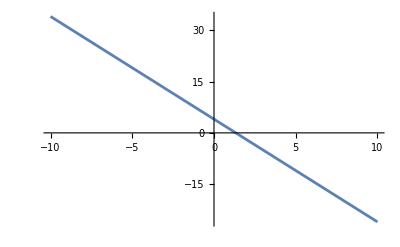

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=a*x
```

a x

```mathematica
g[x_]=c*x+d
```

d+c x

```mathematica
Reduce[f[g[x]]==g[f[x]],x]
```

a==1||d==0

```mathematica
h[x_]=Piecewise[{{(357/101)*x+(47/111),x<=0},{2*x-1, x>0}}]
```

Piecewise[{{47/111+(357 x)/101, x≤0}, {-1+2 x, x>0}, {0, True}}]

```mathematica
h[-1/2]
```

-30133/22422

```mathematica
h[1]
```

1

```mathematica
FactorInteger[10848]
```

{{2,5},{3,1},{113,1}}

```mathematica
Solve[(Binomial[n,3]*3!)==(Binomial[n,4]*4!),n]
```

{{n→0},{n→1},{n→2},{n→4}}

```mathematica
Binomial[100,5]
```

75287520

```mathematica
GCD[177650,101898]
```

34

```mathematica
LCM[177650,101898]
```

532417050

```mathematica
Divisors[10848]
```

{1,2,3,4,6,8,12,16,24,32,48,96,113,226,339,452,678,904,1356,1808,2712,3616,5424,10848}

## combinatorics